```mathematica
(*su(3) fastVersion*)
ClearAll["Global`*"];
t=1;
a=1;
nn=200;
dk=2*Pi/a/nn;
nOfcell=nn*nn;(*num of cells*)
λ[1]={{0,1,0},{1,0,0},{0,0,0}};
λ[2]={{0,-I,0},{I,0,0},{0,0,0}};
λ[3]={{1,0,0},{0,-1,0},{0,0,0}};
λ[4]={{0,0,1},{0,0,0},{1,0,0}};
λ[5]={{0,0,-I},{0,0,0},{I,0,0}};
λ[6]={{0,0,0},{0,0,1},{0,1,0}};
λ[7]={{0,0,0},{0,0,-I},{0,I,0}};
λ[8]=1/Sqrt[3]{{1,0,0},{0,1,0},{0,0,-2}};(*Gell Mann Matrix*)
Table[Λ[i,1]=ArrayFlatten@{{λ[i],0,0},{0,0λ[i],0},{0,0,0λ[i]}}; ,{i,1,8}];(*site A*)
Table[Λ[i,2]=ArrayFlatten@{{0 λ[i],0,0},{0,λ[i],0},{0,0,0λ[i]}}; ,{i,1,8}];(*site B*)
Table[Λ[i,3]=ArrayFlatten@{{0 λ[i],0,0},{0,0λ[i],0},{0,0,λ[i]}}; ,{i,1,8}];(*site C*)
sumVec={1,1,1,1,1,0,0,0,0};
GVec={λ[1],λ[2],λ[3],λ[4],λ[5],λ[6],λ[7],λ[8]};
mag = N[Table[RandomReal[{-1,1}],{i,1,3},{j,1,8}],4];
mkk[mag0_,U0_]:=
Re@Module[{mag=mag0,U=U0,HkMF,uniMat},
ParallelSum[
HkMF=N[-ArrayFlatten[{
{2 3/4U Dot[mag[[1]],GVec],t Cos[kx a/2]IdentityMatrix[3],t Cos[ky a/2]IdentityMatrix[3]},
{t Cos[kx a/2]IdentityMatrix[3],2 3/4 U Dot[mag[[2]],GVec],0},
{t Cos[ky a/2] IdentityMatrix[3],0,2 3/4U Dot[mag[[3]],GVec]}}],4];
uniMat=(SortBy[Eigensystem@HkMF//Transpose,First]//Transpose)[[2]]//Transpose;
{{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[4,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[5,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[6,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[7,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[8,1],uniMat],sumVec]
},
{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[4,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[5,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[6,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[7,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[8,2],uniMat],sumVec]
},
{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[4,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[5,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[6,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[7,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[8,3],uniMat],sumVec]
}},{kx,0,2Pi/a,dk},{ky,0,2Pi/a,dk}]/nOfcell/2];
```

```mathematica
Do[
mm[U]=FixedPoint[mkk[#,U]&,mag,10];
mag=mm[U];
Print[U],{U,0,5,0.2}]
```

0.

0.2

0.4

0.6

0.8

1.

1.2

1.4

1.6

1.8

2.

2.2

2.4

2.6

2.8

3.

3.2

3.4

3.6

3.8

4.

4.2

4.4

4.6

4.8

5.

```mathematica
N[1/Sqrt[3]]
```

0.57735

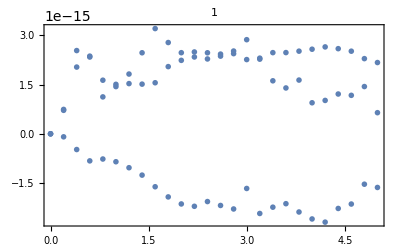
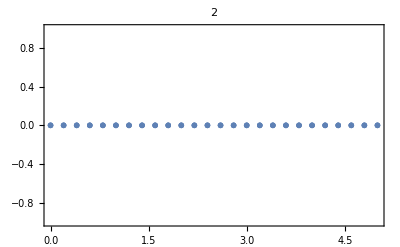
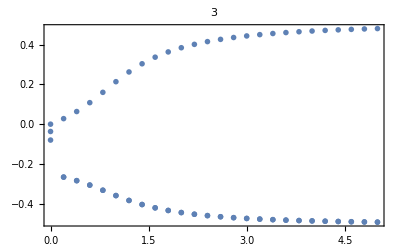
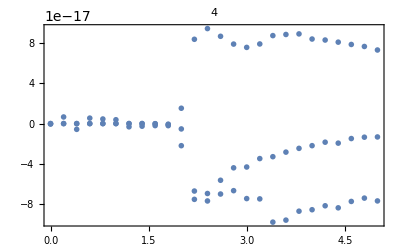
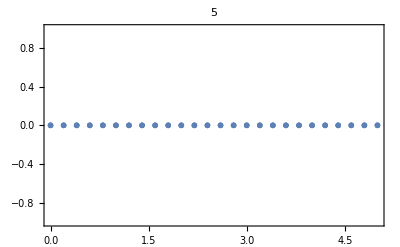
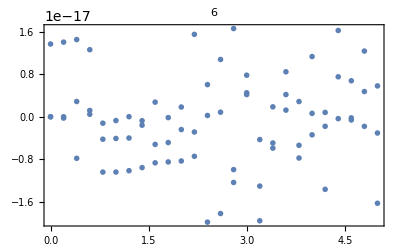
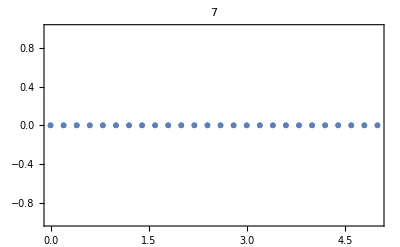
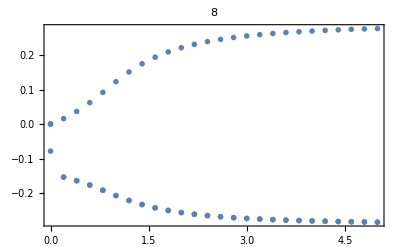

```mathematica
Table[Show[Table[ListPlot[Table[{i*0.2-0.2,Table[Dot[mm[U],{Normal[SparseArray[k->1,8]]}//Transpose],{U,0,5,0.2}][[i,j,1]]},{i,1,26}],PlotMarkers->j],{j,1,3}],PlotRange->All,Frame->True,PlotLabel->k],{k,1,8}]
```

```mathematica
Quit[]
```

```mathematica
Export["SU3e.eps",ListLinePlot[{Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}],-Table[{-U,Norm@mm[U][[2]]},{U,0,5,0.2}],-Table[{-U,Norm@mm[U][[3]]},{U,0,5,0.2}],Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[2]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[3]]},{U,0,5,0.2}]},Frame->True,PlotMarkers->Automatic,PlotLegends->{1,2,3}]]
```

SU3e.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["SU3e.eps"]]]
```

```mathematica
Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[2]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[3]]},{U,0,5,0.2}]
```

{{0.,-0.166582},{0.2,-0.583138},{0.4,-0.583138},{0.6,-0.583138},{0.8,-0.583138},{1.,-0.583138},{1.2,-0.583138},{1.4,-0.583138},{1.6,-0.583138},{1.8,-0.583138},{2.,-0.583138},{2.2,-0.583138},{2.4,-0.583138},{2.6,-0.583138},{2.8,-0.583138},{3.,-0.583138},{3.2,-0.583138},{3.4,-0.583138},{3.6,-0.583138},{3.8,-0.583138},{4.,-0.583138},{4.2,-0.583138},{4.4,-0.583138},{4.6,-0.583138},{4.8,-0.583138},{5.,-0.583138}}

```mathematica
Quit[]
```

```mathematica
mkk[mag,1]//AbsoluteTiming
```

{11.0671,{{0.0239839,-0.226354,0.255396,-0.120535,0.0783199,-0.0843771,-0.157459,-0.243072},{0.190121,-0.306218,0.0544526,-0.190931,0.0436817,0.120873,-0.215414,-0.084622},{-0.10165,0.117714,-0.0417028,-0.347705,-0.0589683,-0.140507,-0.0941157,0.29412}}}

```mathematica
Table[Export["/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU3"<>ToString@k<>".eps",ListLinePlot[Table[Table[{i*0.2-0.2,Table[Dot[mm[U],{Normal[SparseArray[k->1,8]]}//Transpose],{U,0,5,0.2}][[i,j,1]]},{i,1,26}],{j,1,3}],PlotRange->All,Frame->True,PlotLabel->k,FrameLabel->{U,S},PlotMarkers->{Automatic, 7},PlotLegends->{1,2,3},AspectRatio->1/2]],{k,1,8}]
```

{/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU31.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU32.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU33.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU34.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU35.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU36.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU37.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU38.eps}